```mathematica
SetOptions[ {BoxWhiskerChart,Plot,ContourPlot,LogLinearPlot,LogPlot,Histogram,ContourPlot,ContourPlot3D,ListLogLinearPlot,DensityPlot,Plot3D,ParametricPlot,ListLogPlot,ListPlot,ListDensityPlot,ListContourPlot},BaseStyle->{FontFamily->"Helvetica",FontSize->16}];
SetOptions[Plot,PlotStyle->ColorData[1,"ColorList"]];


SetOptions[{BoxWhiskerChart,Plot,ContourPlot,LogLinearPlot,LogPlot,Histogram,ContourPlot,ContourPlot3D,ListLogLinearPlot,DensityPlot,Plot3D,ParametricPlot,ListLogPlot,ListPlot,ListDensityPlot,ListContourPlot},BaseStyle->{FontFamily->"Helvetica",FontSize->16},LabelStyle->{FontFamily->"Helvetica",FontSize->16}];

(*$Messages=$Output;*)
$Messages={};
Needs["PlotLegends`"];
```

## Free energy change of the system

```mathematica
FerCORR2
```

FerCORR2

```mathematica
(* THERMODYNAMIC WORK OF CREATING A CELL WALL FENESTRA *)
```

```mathematica
Fsp=2 π fsp (Rp) L; (* Constricting force of cell plate expansion *)
Fpr=-π Δp (Rp)^2 L;(* Turgor pressure *)
FbendPMnoCORR=π κ L/(Rp);(* Bending enery of PM pore (with no correction for large curvautures) *)

(* This part is to compute the correction to FbendPMnoCORR due to large curvatures - diff. curvatures in the inner vs. outer monolayers *)
Jout=Jmid/(1+Jmid δ);
Jin=-Jmid/(1-Jmid δ);
Aout=Amid (1+Jmid δ);
Ain=Amid (1-Jmid δ);

FbendPM= Simplify[(Aout κ/4 (Jout^2)+Ain κ/4 (Jin^2))/.{Jmid->1/Rp,Amid->2 π Rp L}]; (* Bending enery of PM pore (with correction for large curvautures) *)
FtenPM=2 π σPM (Rp) (L-Rp); (* Plasma membrane tension energy *)

FcellplnoCORR=Fsp+Fpr+FbendPMnoCORR+FtenPM; (* Total free energy per fenestra (without correction for large curvautures) *)
Fcellpl=Fsp+Fpr+FbendPM+FtenPM;(* Total free energy per fenestra (with correction for large curvautures) *)


(* FREE ENERGY CHANGE OF ER DEFORMATION AND MCTP ENRICHMENT AND TETHERING *)

FtenER=2 π L γER (Rt); (* ER membrane tension energy *)

(* The spontaneous curvature of the ER tube - as a function of MCTP concentration - and the equilibrium ER tube radius *)
Clear[Js0];
Js0b=Js0+ζMCTP ϕb; (* Spont. curv. in the bulk ER with a bulk MCTP concentration, ϕb *)
Jst=Js0+ζMCTP ϕt;(* Spont. curv. in the PD tubule ER with an enriched MCTP concentration, ϕt *)
Rer0=2/Js0b (1+Sqrt[1+4 γER/κ/Js0b^2])^(-1); (* bulk ER tube radius *)

(* This part computes the bending energy of the ER tubule *)
FerCORR= π κ L Rt(1/Rt^2-2 Jst (1/Rt-1/Rer0)-1/Rer0^2); (* Bending energy of the ER tube at the bilayer midplane *)
FerCORR2= ((Aout κ/4 (Jout^2-2Jst (Jout-1/Rer0)-1/Rer0^2))+(Ain κ/4 (Jin^2+2Jst (Jin+1/Rer0)-1/Rer0^2)))/.{Jmid->1/Rt,Amid->2 π Rt L};(* Bending enery of PM pore (with correction for large curvautures) *)

Fhyd=π P0 ξh L (2 Rt+2 δ+h) Exp[-h/ξh]; (* Hydration energy *)

FER=Simplify[(FerCORR2)+Fhyd+FtenER]; (* Total free energy change due to presence of an ER tubule (no MCTP enrichment accounted for yet) *)

FERnohyd=Simplify[(FerCORR2)+FtenER]; (* Total free energy change due to presence of an ER tubule (no MCTP enrichment accounted for yet) *)


(* EFFECTS OF MCTP ENRICHMENT AND TETHERING IN PD BRIDGE FORMATION *)

Fent=kbt 2 π Rt L/aMCTP (ϕt Log[ϕt (1-ϕb)/(ϕb (1-ϕt))]+Log[(1-ϕt)/(1-ϕb)]); (* Curvature-mediated sorting of MCTP in he cytoplasmic bridge *)
Fadh=-2 π Rt L ϕt (ϵa0+αJ/(-Rp)) UnitStep[-h+h0];  (* MCTP tethering energy *)

Fdesm=Simplify[(FerCORR2)+Fhyd+Fadh+Fent+FtenER]; (* Total free energy change due to presence of an ER tubule (with MCTP enrichment accounted for) *)


(* TOTAL FREE ENERGY CHANGE OF THE SYSTEM *)

FPD=Simplify[((Fcellpl+Fdesm))/.{Rp->(Rt+2 δ+h)}] (* Total free energy change of the system, as a function of the ER tube radius (Rt), and the cytoplasmic distance between ER and PM (h), as well as the tube MCTP density (ϕt) *)
```

1/2 π (4 fsp L (h+Rt+2 δ)-2 L (h+Rt+2 δ)^2 Δp+(2 L (h+Rt+2 δ) κ)/(-δ^2+(h+Rt+2 δ)^2)-4 (h+Rt+2 δ) (h-L+Rt+2 δ) σPM+L (4 Rt γER+2 ⅇ^(-h/ξh) P0 (h+2 (Rt+δ)) ξh+(Rt+δ) κ (1/(Rt+δ)^2-1/4 (Js0+ζMCTP ϕb)^2 (1+√(1+(4 γER)/(κ (Js0+ζMCTP ϕb)^2)))^2-2 (1/(Rt+δ)-1/2 (Js0+ζMCTP ϕb) (1+√(1+(4 γER)/(κ (Js0+ζMCTP ϕb)^2)))) (Js0+ζMCTP ϕt))+Rt (1-δ/Rt) κ (1/(Rt-δ)^2-1/4 (Js0+ζMCTP ϕb)^2 (1+√(1+(4 γER)/(κ (Js0+ζMCTP ϕb)^2)))^2+2 (1/(-Rt+δ)+1/2 (Js0+ζMCTP ϕb) (1+√(1+(4 γER)/(κ (Js0+ζMCTP ϕb)^2)))) (Js0+ζMCTP ϕt))+(4 kbt Rt (Log[(-1+ϕt)/(-1+ϕb)]+ϕt Log[((-1+ϕb) ϕt)/(ϕb (-1+ϕt))]))/aMCTP-4 Rt (-αJ/(h+Rt+2 δ)+ϵa0) ϕt UnitStep[-h+h0]))

## Free energy parameters

```mathematica
(*
Distances in nm;
Energies in pN·nm;
Forces in pN;
*)

parsTOT={L->150,fsp->10, Δp->0.2,σPM->0.1,κ->80,ξh->0.25,P0->200,δ->2,γER->0.012,Js0->0.036,ϕb->0.001,aMCTP->10,kbt->4.11,h0->10,ϵa0->10,ζMCTP->0.5,αJ->4.11 (-0)};  (* Parameters used for the paper *)
```

## Results

### Initial plots showing the behavior of the free energy terms

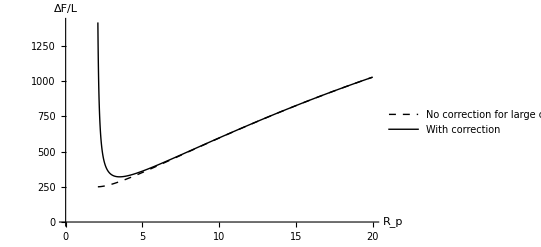

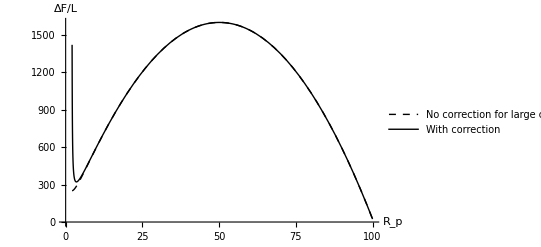

```mathematica
(* This is the free energy of the PM fenestra,where a correction for short radius (large curvatures) is included,showing the divergence of the free energy when the radius is close to the monolayer thickness *)

Plot[{(FcellplnoCORR/L)/.parsTOT,(Fcellpl/L)/.parsTOT},{Rp,2.1,20},AxesOrigin->{0,0},PlotStyle->{{Black,Thick,Dashed},{Black,Thick}},AxesLabel->{"R_p","ΔF/L"},PlotLegends->{"No correction for large curvatures","With correction"}] 

Plot[{(FcellplnoCORR/L)/.parsTOT,(Fcellpl/L)/.parsTOT},{Rp,2.1,100},AxesOrigin->{0,0},PlotStyle->{{Black,Thick,Dashed},{Black,Thick}},AxesLabel->{"R_p","ΔF/L"},PlotLegends->{"No correction for large curvatures","With correction"}]
```

```mathematica
(Fent/L)/.parsTOT
```

2.58239 Rt (Log[1.001 (1-ϕt)]+ϕt Log[(999. ϕt)/(1-ϕt)])

```mathematica
parsTOT
```

{L→150,fsp→10,Δp→0.2,σPM→0.1,κ→80,ξh→0.25,P0→200,δ→2,γER→0.012,Js0→0.036,ϕb→0.001,aMCTP→10,kbt→4.11,h0→10,ϵa0→10,ζMCTP→0.5,αJ→0.}

```mathematica
(Fadh/L)/.parsTOT/.{ϕt->0.01}
```

-0.628319 Rt UnitStep[10-h]

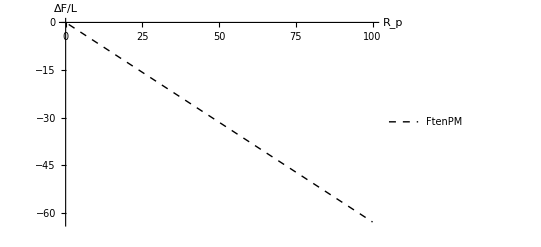

```mathematica
Plot[{(Fadh/L)/.parsTOT/.{ϕt->0.01,h->5}},{Rt,1,100},AxesOrigin->{0,0},PlotStyle->{{Black,Thick,Dashed},{Black,Thick}},AxesLabel->{"R_p","ΔF/L"},PlotLegends->{"FtenPM"}]
```

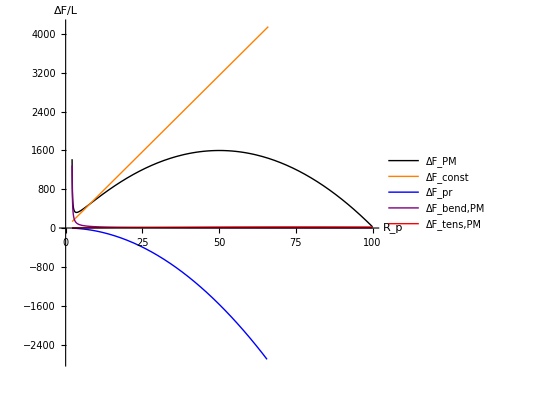

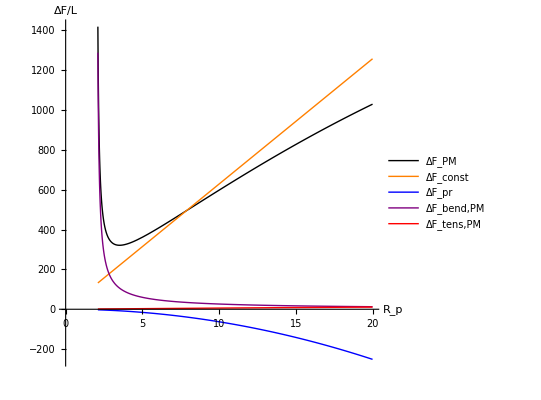

{sNEWa1.txt,sNEWa2.txt,sNEWa3.txt,sNEWa4.txt,sNEWa5.txt}

```mathematica
(* This is the energy of the PM fenestra (ΔF_PM), split over the different contributions (constricting force energy, turgor pressure,bending,and tension). One can see that the tension energy (red) is almost negligible,and that the main contributions arise from the constricting force (orange), leading to sealing; the pressure force (blue), preventing sealing; and the bending energy (purple), which only plays a significan role for very narrow pores, when it prevents fenestra closure *)

Plot[{(Fcellpl/L)/.parsTOT,(Fsp/L)/.parsTOT,(Fpr/L)/.parsTOT,(FbendPM/L)/.parsTOT,(FtenPM/L)/.parsTOT},{Rp,2.1,100},AxesOrigin->{0,0},PlotStyle->{{Black,Thick},{Orange,Thick},{Blue,Thick},{Purple,Thick},{Red,Thick}}(*,PlotRange->{-100,100}*),PlotLegends->{"ΔF_PM","ΔF_const","ΔF_pr","ΔF_bend,PM","ΔF_tens,PM"},AspectRatio->1,AxesLabel->{"R_p","ΔF/L"}]

sNEWa=Plot[{(Fcellpl/L)/.parsTOT,(Fsp/L)/.parsTOT,(Fpr/L)/.parsTOT,(FbendPM/L)/.parsTOT,(FtenPM/L)/.parsTOT},{Rp,2.1,20},AxesOrigin->{0,0},PlotStyle->{{Black,Thick},{Orange,Thick},{Blue,Thick},{Purple,Thick},{Red,Thick}}(*,PlotRange->{-100,100}*),PlotLegends->{"ΔF_PM","ΔF_const","ΔF_pr","ΔF_bend,PM","ΔF_tens,PM"},AspectRatio->1,AxesLabel->{"R_p","ΔF/L"}]

multidat=Cases[First@sNEWa,Line[data_]:>data,-4];
Export["sNEWa"<>IntegerString[#2]<>".txt",#,"Table"]&~MapIndexed~multidat
```

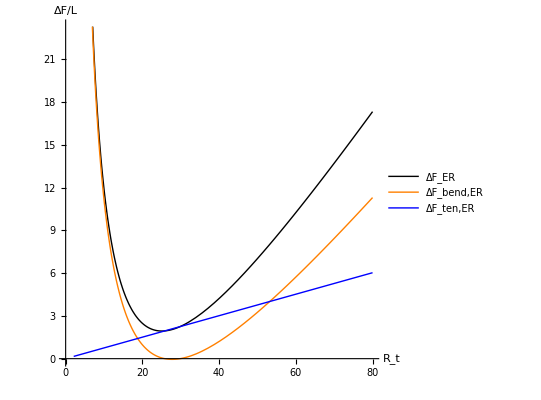

{sNEWb1.txt,sNEWb2.txt,sNEWb3.txt}

```mathematica
(* This is the energy of the ER desmotubule (per unit length of the tubules), without considering any enrichment of MCTPs or any interaction (no tethering) with the PM. One can see that tension promotes tube shrinking,whereas curvature promotes a certain finite radius size (which depends on the ER spontaneous curvature) *)

sNEWb=Plot[{((Fdesm/L)/.{h->1000,ϕt->ϕb})/.parsTOT,((FerCORR2/L)/.{h->1000,ϕt->ϕb})/.parsTOT,((FtenER/L)/.{h->1000,ϕt->ϕb})/.parsTOT},{Rt,2.1,80},AxesOrigin->{0,0},PlotStyle->{{Black,Thick},{Orange,Thick},{Blue,Thick},{Purple,Thick},{Red,Thick}}(*,PlotRange->{-100,100}*),PlotLegends->{"ΔF_ER","ΔF_bend,ER","ΔF_ten,ER","ΔF_bend,PM","ΔF_tens,PM"},AspectRatio->1,AxesLabel->{"R_t","ΔF/L"}]


multidat=Cases[First@sNEWb,Line[data_]:>data,-4];
Export["sNEWb"<>IntegerString[#2]<>".txt",#,"Table"]&~MapIndexed~multidat
```

```mathematica
sNEWb=Plot[{(((FerCORR2+FtenER)/L)/.{ϕt->ϕb})/.parsTOT,((FerCORR2/L)/.{ϕt->ϕb})/.parsTOT,((FtenER/L)/.{ϕt->ϕb})/.parsTOT},{Rt,2.1,80},AxesOrigin->{0,0},PlotStyle->{{Black,Thick},{Orange,Thick},{Blue,Thick},{Purple,Thick},{Red,Thick}}(*,PlotRange->{-100,100}*),PlotLegends->{"ΔF_ER","ΔF_bend,ER","ΔF_ten,ER","ΔF_bend,PM","ΔF_tens,PM"},AspectRatio->1,AxesLabel->{"R_t","ΔF/L"}]


multidat=Cases[First@sNEWb,Line[data_]:>data,-4];
Export["sNEWb"<>IntegerString[#2]<>".txt",#,"Table"]&~MapIndexed~multidat
```

-Graphics-

{sNEWb1.txt,sNEWb2.txt,sNEWb3.txt}

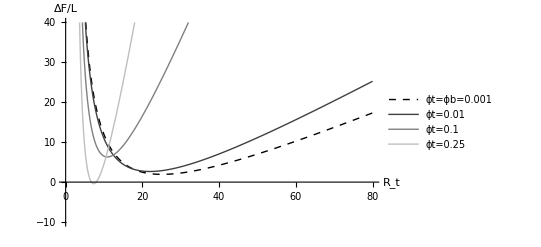

```mathematica
(* Effect of MCTP enrichment on ER tubule energy;Now we take from the previous graph the black curve corresponding to the energy of the ER desmotubule without enrichment of MCTPs and without interaction (no tethering) with the PM (new dashed black curve). And we add to it the effect of MCTP enrichment in the tubule. One can see how this curve changes when we artificially ”increase” the concentration of MCTPs (ϕt) in the tube. Now,because we have enrichment of MCTPs in the tube (ϕt>ϕb), we need to take into account the entropy of partitioning (ΔF_ent) *)

Plot[{((Fdesm/L)/.{h->1000,ϕt->ϕb})/.parsTOT,((Fdesm/L)/.{h->1000,ϕt->0.01})/.parsTOT,((Fdesm/L)/.{h->1000,ϕt->0.1})/.parsTOT,((Fdesm/L)/.{h->1000,ϕt->0.25})/.parsTOT},{Rt,2.1,80},AxesOrigin->{0,0},PlotStyle->{{Black,Thick,Dashed},{GrayLevel[.25],Thick},{GrayLevel[.5],Thick},{GrayLevel[.75],Thick}}(*,PlotRange->{-100,100}*),PlotLegends->{"ϕt=ϕb=0.001","ϕt=0.01","ϕt=0.1","ϕt=0.25"},AxesLabel->{"R_t","ΔF/L"},PlotRange->{-10,40}]
```

```mathematica
(* We now numerically find the local minimum of the ER tubule energy (at small Rt values), the following is an example for a given ϕt *)
FindMinimum[(Fdesm/L)/.{h->1000,ϕt->0.1}/.parsTOT/.{Rt->x},{x,2.5}]
```

{6.29501,{x→10.8732}}

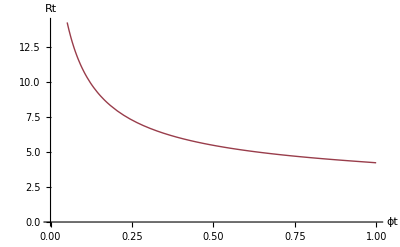

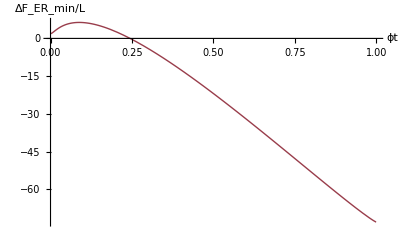

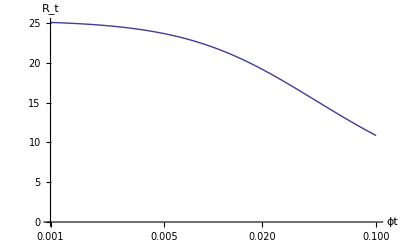

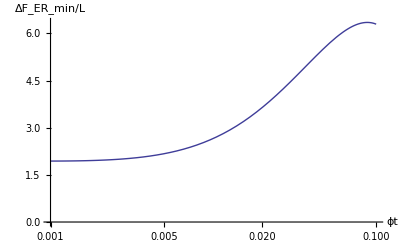

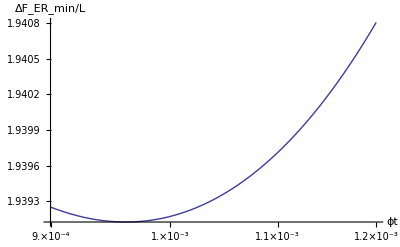

```mathematica
(* We next look for the minimum of the ER tube energy (remember,no PM here yet), and see how that changes with the concentration of MCTPs. We can compute the free energy of the minimum and see how that changes with the concentration (showing that there is no spontaneous enrichment of MCTPs in the tube),and the optimal tube radius as a function of the MCTP concentration *)

Plot[x/.FindMinimum[(Fdesm/L)/.{h->1000,ϕt->y}/.parsTOT/.{Rt->x},{x,2.5}][[2]],{y,0.001,1},AxesOrigin->{0,0},AxesLabel->{"ϕt","Rt"}]
Plot[FindMinimum[(Fdesm/L)/.{h->1000,ϕt->y}/.parsTOT/.{Rt->x},{x,2.5}][[1]],{y,0.001,1},AxesOrigin->{0,0},AxesLabel->{"ϕt","ΔF_ER_min/L"}]
LogLinearPlot[x/.FindMinimum[(Fdesm/L)/.{h->1000,ϕt->y}/.parsTOT/.{Rt->x},{x,2.5}][[2]],{y,0.001,0.1},AxesOrigin->{0.001,0},AxesLabel->{"ϕt","R_t"}]
LogLinearPlot[FindMinimum[(Fdesm/L)/.{h->1000,ϕt->y}/.parsTOT/.{Rt->x},{x,2.5}][[1]],{y,0.001,0.1},AxesOrigin->{0.001,0},AxesLabel->{"ϕt","ΔF_ER_min/L"}]
LogLinearPlot[FindMinimum[(Fdesm/L)/.{h->1000,ϕt->y}/.parsTOT/.{Rt->x},{x,2.5}][[1]],{y,0.0009,0.0012},AxesLabel->{"ϕt","ΔF_ER_min/L"},Ticks->{{#,ScientificForm@#} & /@ Range[0.0008,0.0012,0.0001],Automatic}]
```

```mathematica
(* Same thing, done in a different way - COMMENTED *)

(*
RtminTUBE=Rt/.Solve[D[Limit[(((Fdesm/L)/.{ϕt->y})/.parsTOT),h->∞],Rt]==0,Rt][[4]];
Plot[RtminTUBE,{y,0.001,0.25}]
LogLinearPlot[(Limit[(((Fdesm/L)/.{ϕt->y})/.parsTOT),h->∞]/.{Rt->RtminTUBE})/.parsTOT,{y,0.001,0.25}]
Plot[(Limit[(((Fdesm/L)/.{ϕt->y})/.parsTOT),h->∞]/.{Rt->RtminTUBE})/.parsTOT,{y,0.0001,0.25}]
Plot[Chop[D[((Limit[(((Fdesm/L)/.{ϕt->y})/.parsTOT),h->∞]/.{Rt->RtminTUBE})/.parsTOT),y]]/.{y->yyy},{yyy,0.0001,0.01}]
*)
```

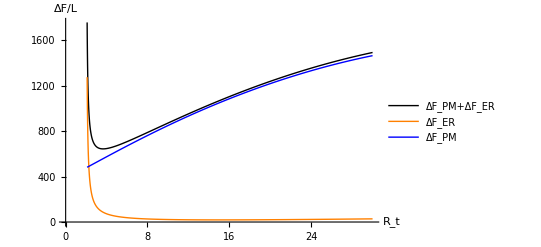

```mathematica
(* We now plot the total free energy change of the system (PM+ER tubule),and split it in the two contributions (PM and ER).This is for the case of no tethering (ϵa0=0) and no MCTP enrichment (ϕt=ϕb). For illustrative purposes, we consider here that ER and PM are very close together (h=1.5 nm) *)

Plot[{(FPD/L)/.{ϵa0->0,h->1.5,ϕt->ϕb}/.parsTOT,(Fdesm/L)/.{ϵa0->0,h->1.5,ϕt->ϕb}/.parsTOT,(Fcellpl/L)/.{Rp->Rt+2 δ+h}/.{ϵa0->0,h->1.5,ϕt->ϕb}/.parsTOT},{Rt,2.1,30},AxesOrigin->{0,0},PlotStyle->{{Black,Thick},{Orange,Thick},{Blue,Thick}}(*,PlotRange->{-100,100}*),PlotLegends->{"ΔF_PM+ΔF_ER","ΔF_ER","ΔF_PM","ϕt=0.25"},AxesLabel->{"R_t","ΔF/L"},PlotRange->Automatic]
```

```mathematica
Plot[{(FPD/L)/.{ϵa0->0,h->1.5,ϕt->ϕb}/.parsTOT,(Fdesm/L)/.{ϵa0->0,h->1.5,ϕt->ϕb}/.parsTOT,(Fcellpl/L)/.{Rp->Rt+2 δ+h}/.{ϵa0->0,h->1.5,ϕt->ϕb}/.parsTOT},{Rt,2.1,30},AxesOrigin->{0,0},PlotStyle->{{Black,Thick},{Orange,Thick},{Blue,Thick}}(*,PlotRange->{-100,100}*),PlotLegends->{"ΔF_PM+ΔF_ER","ΔF_ER","ΔF_PM","ϕt=0.25"},AxesLabel->{"R_t","ΔF/L"},PlotRange->Automatic]
```

### Results for the case of no MCTP enrichment and no MCTP tethering

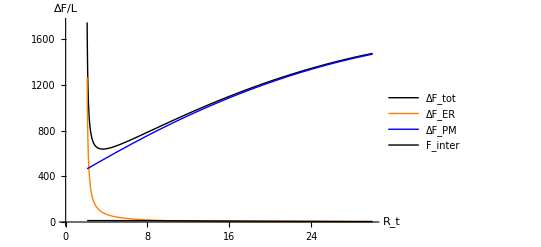

{sNEWc11.txt,sNEWc12.txt,sNEWc13.txt,sNEWc14.txt}

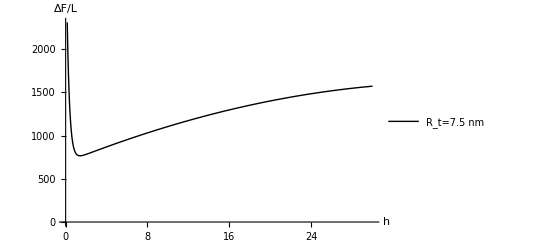

{sNEWc21.txt}

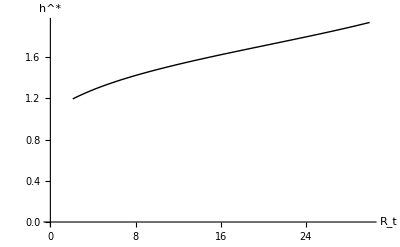

{sNEWc31.txt}

```mathematica
(* So,the next step is to release the constraint of fixed ”h” (fixed distance between the PM and the ER membrane),that we used in the previous plot for illustrative purposes. Now,for each “R_t”, we need to find the value of "h" that minimizes the total free energy *)

sNEWc1=Plot[{FindMinimum[(FPD/L)/.{ϵa0->0,ϕt->ϕb}/.parsTOT,{h,1.5}][[1]],(FERnohyd/L)/.{ϵa0->0,h->(h/.(FindMinimum[(FPD/L)/.{ϵa0->0,ϕt->ϕb}/.parsTOT,{h,1.5}][[2]])),ϕt->ϕb}/.parsTOT,(Fcellpl/L)/.{Rp->Rt+2 δ+h}/.{ϵa0->0,h->(h/.(FindMinimum[(FPD/L)/.{ϵa0->0,ϕt->ϕb}/.parsTOT,{h,1.5}][[2]])),ϕt->ϕb}/.parsTOT,(Fhyd/L)/.{ϵa0->0,h->(h/.(FindMinimum[(FPD/L)/.{ϵa0->0,ϕt->ϕb}/.parsTOT,{h,1.5}][[2]])),ϕt->ϕb}/.parsTOT},{Rt,2.1,30},AxesOrigin->{0,0},PlotStyle->{{Black,Thick},{Orange,Thick},{Blue,Thick}}(*,PlotRange->{-100,100}*),PlotLegends->{"ΔF_tot","ΔF_ER","ΔF_PM","F_inter","ϕt=0.25"},AxesLabel->{"R_t","ΔF/L"},PlotRange->Automatic]
(* One can see that this first plot is very similar to the one in the previous plot,basically because the ”guess” of h=1.5nm used before is very close to the optimal h (computed by minimizing the energy),as calculated by the model (see other figures) *)

multidat=Cases[First@sNEWc1,Line[data_]:>data,-4];
Export["sNEWc1"<>IntegerString[#2]<>".txt",#,"Table"]&~MapIndexed~multidat

sNEWc2=Plot[{(FPD/L)/.{ϵa0->0,ϕt->ϕb}/.parsTOT/.{Rt->7.5}},{h,0,30},AxesOrigin->{0,0},PlotStyle->{{Black,Thick},{Orange,Thick},{Blue,Thick}}(*,PlotRange->{-100,100}*),PlotLegends->{"R_t=7.5 nm"},AxesLabel->{"h","ΔF/L"},PlotRange->Automatic]
(* This plot shows that, for a given value of the ER tube radius, Rt, the free energy profile, when plotted against "h" has a local minimum at a small value of "h", which is the one that optimizes the overall free energy of the system *)

multidat=Cases[First@sNEWc2,Line[data_]:>data,-4];
Export["sNEWc2"<>IntegerString[#2]<>".txt",#,"Table"]&~MapIndexed~multidat

sNEWc3=Plot[{h/.FindMinimum[(FPD/L)/.{ϵa0->0,ϕt->ϕb}/.parsTOT,{h,1.5}][[2]]},{Rt,2.1,30},AxesOrigin->{0,0},PlotStyle->{{Black,Thick},{Orange,Thick},{Blue,Thick}}(*,PlotRange->{-100,100}*),AxesLabel->{"R_t","h^*"},PlotRange->Automatic]
(* This plot shows the optimal ER-PM distance as a function of the ER tubule radius *)

multidat=Cases[First@sNEWc3,Line[data_]:>data,-4];
Export["sNEWc3"<>IntegerString[#2]<>".txt",#,"Table"]&~MapIndexed~multidat
```

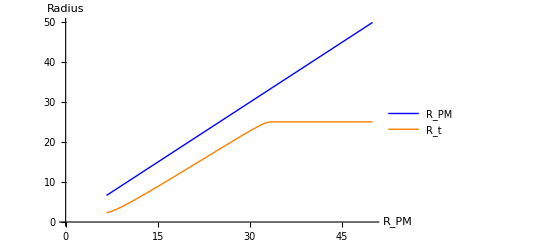

{sNEWe1.txt,sNEWe2.txt}

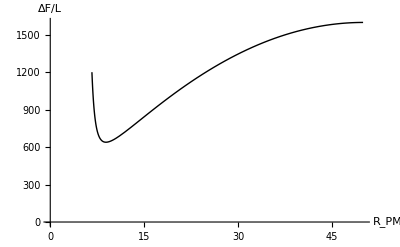

```mathematica
(* Hence, this is a summary of this first part of results (no MCTP enrichment and no tethering).
First plot: This shows how the optimal ER tubule radius (orange curve) changes when the PM fenestra is closing (blue line). One can see that for broad fenestrae (R_PM>32 nm),the ER tubule keeps the optimal ER tube radius (25 nm), but as long as the fenestra starts to close further, then the ER tubule shrinks (keeping a distance h of around 1.5nm).
Second plot:t his is again the same plot as in a previous section, showing the optimal free energy per unit length of the PD, plotted as a function of the PM fenestra radius. One can see that there is an optimal fenestra radius, for this set of parameters corresponding to ~9.5nm. *)

ϕtpar=ϕb;
ϵa0par=0;

sNEWe=Plot[{x,(x-(2 δ)/.parsTOT)-(h/.FindMinimum[((FPD/L)/.{Rt->Rp-2 δ-h})/.{ϵa0->ϵa0par,ϕt->ϕtpar,Rp->x}/.parsTOT,{h,(0.15+0 (x-30) UnitStep[x-30])}][[2]])},{x,6.66,50},AxesOrigin->{0,0},AxesLabel->{"R_PM","Radius"},PlotLegends->{"R_PM","R_t"},PlotStyle->{{Blue,Thick},{Orange,Thick}},PlotRange->{0,50}]

multidat=Cases[First@sNEWe,Line[data_]:>data,-4];
Export["sNEWe"<>IntegerString[#2]<>".txt",#,"Table"]&~MapIndexed~multidat

Plot[{(FindMinimum[((FPD/L)/.{Rt->Rp-2 δ-h})/.{ϵa0->ϵa0par,ϕt->ϕtpar,Rp->x}/.parsTOT,{h,(0.15+0 (x-30) UnitStep[x-30])}][[1]])},{x,6.66,50},AxesOrigin->{0,0},AxesLabel->{"R_PM","ΔF/L"},PlotStyle->{{Black,Thick},{Orange,Thick}},PlotRange->Automatic]

Clear[ϕtpar,ϵa0par];
```

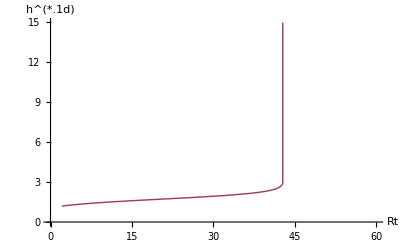

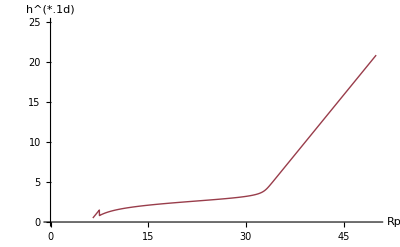

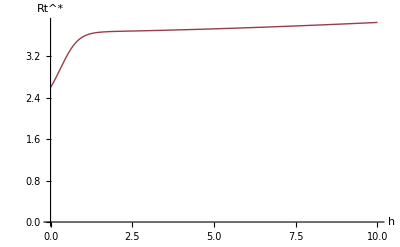

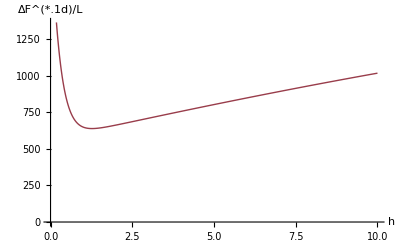

```mathematica
(* Some other related plots *)
ϕtpar=ϕb;
ϵa0par=0;
Plot[y/.FindMinimum[(FPD/L)/.{ϵa0->ϵa0par,h->y,ϕt->ϕtpar}/.parsTOT/.{Rt->x},{y,1.5}][[2]],{x,2.1,60},AxesOrigin->{0,0},PlotRange->{0,15}, AxesLabel->{"Rt","h^(*.1d)"}]
Plot[Chop[y/.FindMinimum[((FPD/L)/.{Rt->Rp-2 δ-h})/.{ϵa0->ϵa0par,h->y,ϕt->ϕtpar}/.parsTOT/.{Rp->x},{y,1.5}][[2]]],{x,6.5,50},AxesOrigin->{0,0},PlotRange->{0,25}, AxesLabel->{"Rp","h^(*.1d)"}]
Plot[x/.FindMinimum[(FPD/L)/.{ϵa0->ϵa0par,h->y,ϕt->ϕtpar}/.parsTOT/.{Rt->x},{x,2.5}][[2]],{y,0.,10},AxesOrigin->{0,0}, AxesLabel->{"h","Rt^*"}]
Plot[FindMinimum[(FPD/L)/.{ϵa0->ϵa0par,h->y,ϕt->ϕtpar}/.parsTOT/.{Rt->x},{x,2.5}][[1]],{y,0.,10},AxesOrigin->{0,0}, AxesLabel->{"h","ΔF^(*.1d)/L"}]
Clear[ϕtpar,ϵa0par];
```

### Results for the case with MCTP enrichment and MCTP tethering

```mathematica
(* Now we can start adding complexity to the system, meaning we can add the possibility for enrichment of MCTPs at the ER tubule and adding ”functions” to these MCTPs:;

(1) the fact that they can stabilize/sense ER curvature (curvature sensing);
(2) that they can bind the PM PI4P (TETHERING);

This means that to start with we have a new parameter to optimize (so far we had two: the radius of the ER tube (R_t),and the distance between the ER and the PM (h). Now we have an extra one,which is the concentration of MCTPs on the DT (ϕ_t) *)
```

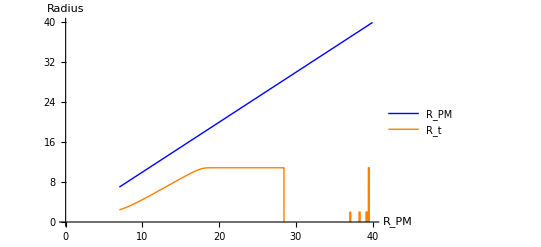

```mathematica
(* First example, where ϕt>ϕb (manually selected) *)
ϕtpar=0.1;
ϵa0par=0;

Plot[{x,Chop[(x-(2 δ)/.parsTOT)-(h/.FindMinimum[((FPD/L)/.{Rt->Rp-2 δ-h})/.{ϵa0->ϵa0par,ϕt->ϕtpar,Rp->x}/.parsTOT,{h,(0.5+0 (x-18) UnitStep[x-18])}][[2]])]},{x,7,40},AxesOrigin->{0,0},AxesLabel->{"R_PM","Radius"},PlotLegends->{"R_PM","R_t"},PlotStyle->{{Blue,Thick},{Orange,Thick}},PlotRange->{0,40}]

Clear[ϕtpar,ϵa0par];
```

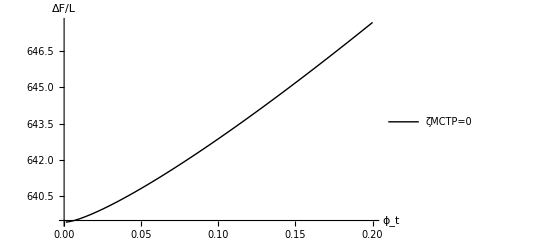

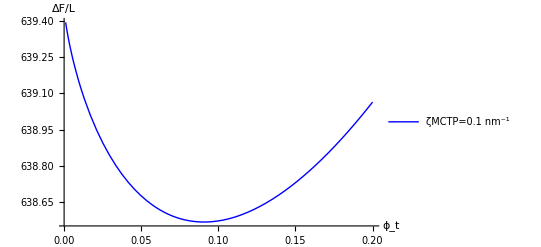

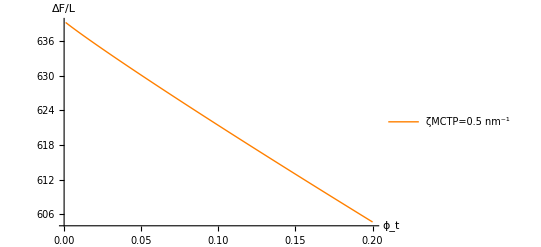

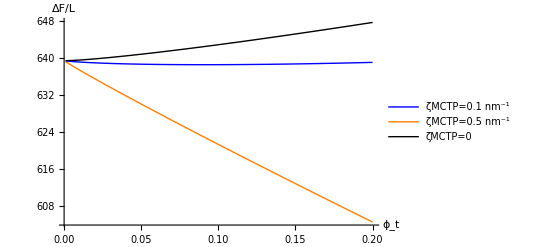

```mathematica
(* Let’s start we testing the effect of the curvature sensitivity (withouth tethering). Below, there are 3 examples of how the free energy profile looks like as a function of the concentration of MCTPs on the ER tubule.;
First plot: energy increases when phi_t increases,so no curvature sorting;
Second plot: energy decreases when phi_t increases,so complete curvature sorting;
Third plot: energy has a minimum for a certain ϕ_t,so partial sorting. *)
Plot[{FindMinimum[{((FPD/L)/.{ζMCTP->0.0,ϵa0->0})/.parsTOT,Rt>2,h>0},{{h,1},{Rt,2.5}}][[1]]},{ϕt,0.001,0.2},AxesLabel->{"ϕ_t","ΔF/L"},PlotStyle->{Black,Thick},PlotLegends->{"ζMCTP=0"},PlotRange->All]
Plot[{FindMinimum[{((FPD/L)/.{ζMCTP->0.1,ϵa0->0})/.parsTOT,Rt>2,h>0},{{h,1},{Rt,2.5}}][[1]]},{ϕt,0.001,0.2},AxesLabel->{"ϕ_t","ΔF/L"},PlotStyle->{Blue,Thick},PlotLegends->{"ζMCTP=0.1 nm^-1"},PlotRange->All]
Plot[{FindMinimum[{((FPD/L)/.{ζMCTP->0.5,ϵa0->0})/.parsTOT,Rt>2,h>0},{{h,1},{Rt,2.5}}][[1]]},{ϕt,0.001,0.2},AxesLabel->{"ϕ_t","ΔF/L"},PlotStyle->{Orange,Thick},PlotLegends->{"ζMCTP=0.5 nm^-1"},PlotRange->All]
Show[%,%%,%%%,PlotRange->All]
```

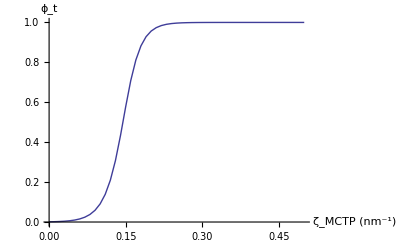

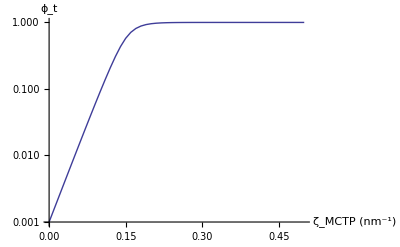

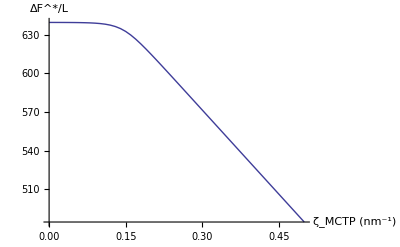

```mathematica
(* So what we do next is to look for the concentration of MCTPs in the ER tubule that minimizes the total free energy of the system (see previous plots) for different values of the curvature induced by MCTPs (same plots,first in linear scale, next in log scale) *)

ListPlot[Table[{zzz,ϕt/.FindMinimum[{((FPD/L)/.{ζMCTP->zzz,ϵa0->0,Rt->Rp-2 δ-h})/.parsTOT,Rp>4,h>0,ϕt≥0,ϕt≤1},{{h,1},{Rp,10},{ϕt,0.1}}][[2]]},{zzz,0,0.5,0.01}],Joined->True,AxesLabel->{"ζ_MCTP (nm^-1)","ϕ_t"}]
ListLogPlot[Table[{zzz,ϕt/.FindMinimum[{((FPD/L)/.{ζMCTP->zzz,ϵa0->0,Rt->Rp-2 δ-h})/.parsTOT,Rp>4,h>0,ϕt≥0,ϕt≤1},{{h,1},{Rp,10},{ϕt,0.1}}][[2]]},{zzz,0,0.5,0.01}],Joined->True,AxesLabel->{"ζ_MCTP (nm^-1)","ϕ_t"}]

(* And the corresponding free energy of the locally metastable state as a function of MCTP induced curvature. We see that the energy goes down with increasing curvature,meaning that the ability of MCTP to sense curvature is indeed a stabilizing factor for PD structures *)
ListPlot[Table[{zzz,FindMinimum[{((FPD/L)/.{ζMCTP->zzz,ϵa0->0,Rt->Rp-2 δ-h})/.parsTOT,Rp>4,h>0,ϕt≥0,ϕt≤1},{{h,1},{Rp,10},{ϕt,0.1}}][[1]]},{zzz,0,0.5,0.01}],Joined->True,AxesLabel->{"ζ_MCTP (nm^-1)","ΔF^*/L"}]
```

```mathematica
(* NOTE:from now on,we limit the maximum coverage of MCTPs on the DT to 10% (phi_t=0.1).Also,for larger values; the entropic part of the free energy is not fully realistic (the entropic part of the free energy assumes that the enrichment is not massive). *)
```

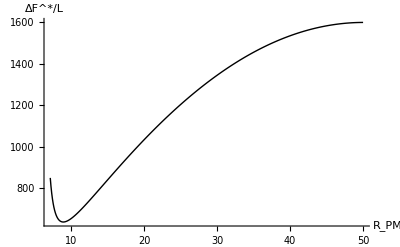

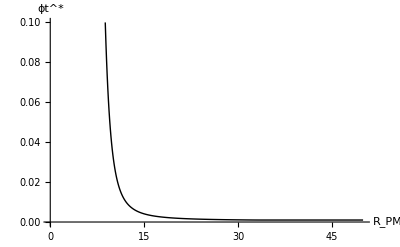

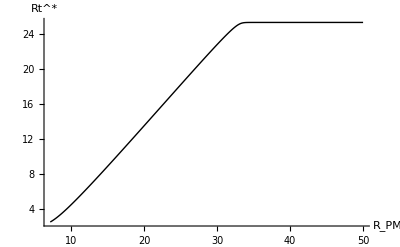

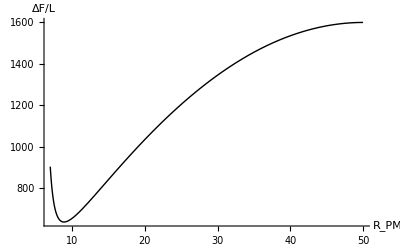

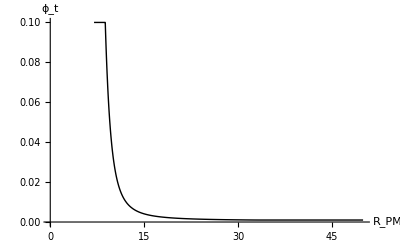

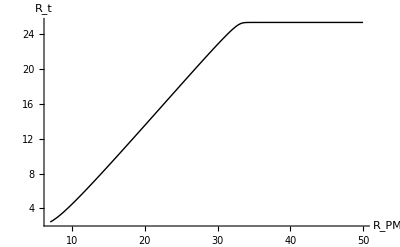

```mathematica
(* Now, we can proceed as before, and compute for each PM pore radius what is the configuration, in this case,the distance between PM and ER (h); and the concentration of MCTP at the tube (ϕ_t) and compute the optimal energy as a function of fenestra size *)
ListPlot[Table[{zzz,FindMinimum[{((FPD/L)/.{ζMCTP->0.1,ϵa0->0,Rt->zzz-2 δ-h})/.parsTOT,h>0,ϕt≥0,ϕt≤1},{{h,1.},{ϕt,0.1}}][[1]]},{zzz,7,50,0.1}],Joined->True,AxesLabel->{"R_PM","ΔF^*/L"},PlotRange->All,AxesOrigin->{0,0},PlotStyle->Black,PlotLegends->"ζMCTP=0.1 nm^-1"]

ListPlot[Table[{zzz,ϕt/.FindMinimum[{((FPD/L)/.{ζMCTP->0.1,ϵa0->0,Rt->zzz-2 δ-h})/.parsTOT,h>0,ϕt≥0,ϕt≤1},{{h,1.},{ϕt,0.1}}][[2]]},{zzz,7,50,0.1}],Joined->True,AxesLabel->{"R_PM","ϕt^*"},AxesOrigin->{0,0},PlotStyle->Black,PlotRange->{0,0.1}]
ListPlot[Table[{zzz,((zzz-2 δ)/.parsTOT)-(h/.FindMinimum[{((FPD/L)/.{ζMCTP->0.1,ϵa0->0,Rt->zzz-2 δ-h})/.parsTOT,h>0,ϕt≥0,ϕt≤1},{{h,1.},{ϕt,0.1}}][[2]])},{zzz,7,50,0.1}],Joined->True,AxesLabel->{"R_PM","Rt^*"},AxesOrigin->{0,0},PlotStyle->Black,PlotRange->All]

(*THIS IS A BETTER WAY OF NUMERICAL MINIMIZATION, in which we also set some limits to the max value of ϕt (ϕt≤0.1) *)
Plot[NMinimize[{(FPD/L)/.{ζMCTP->0.1,ϵa0->0,Rt->(RPM-2 δ-h)}/.parsTOT,0<h<(RPM-6),0≤ϕt≤0.1},{h,ϕt},Method->{"RandomSearch","SearchPoints"->10}][[1]],{RPM,7,50},AxesLabel->{"R_PM","ΔF/L"},AxesOrigin->{0,0},PlotStyle->Black,PlotRange->All,PlotLegends->"ζMCTP=0.1 nm^-1"]

Plot[ϕt/.NMinimize[{(FPD/L)/.{ζMCTP->0.1,ϵa0->0,Rt->(RPM-2 δ-h)}/.parsTOT,0<h<(RPM-6),0≤ϕt≤0.1},{h,ϕt},Method->{"RandomSearch","SearchPoints"->50}][[2]],{RPM,7,50},AxesLabel->{"R_PM","ϕ_t"},AxesOrigin->{0,0},PlotStyle->Black,PlotRange->{0,0.1}]

Plot[((RPM-2 δ )/.parsTOT)-(h/.NMinimize[{(FPD/L)/.{ζMCTP->0.1,ϵa0->0,Rt->(RPM-2 δ-h)}/.parsTOT,0<h<(RPM-6),0≤ϕt≤0.1},{h,ϕt},Method->{"RandomSearch","SearchPoints"->50}][[2]]),{RPM,7,50},AxesLabel->{"R_PM","R_t"},AxesOrigin->{0,0},PlotStyle->Black,PlotRange->All]
```

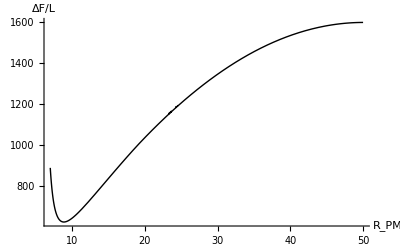

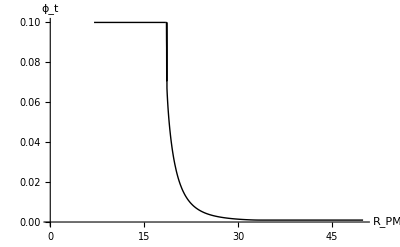

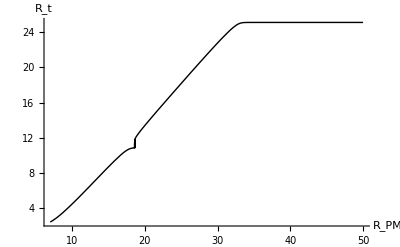

```mathematica
(* Now for a case where MCTPs have a strong curvature generation capability *)
Plot[NMinimize[{(FPD/L)/.{ζMCTP->0.5,ϵa0->0,Rt->(RPM-2 δ-h)}/.parsTOT,0<h<(RPM-6),0≤ϕt≤0.1},{h,ϕt},Method->{"RandomSearch","SearchPoints"->10}][[1]],{RPM,7,50},AxesLabel->{"R_PM","ΔF/L"},AxesOrigin->{0,0},PlotStyle->Black,PlotRange->All,PlotLegends->"ζMCTP=0.5 nm^-1"]

Plot[ϕt/.NMinimize[{(FPD/L)/.{ζMCTP->0.5,ϵa0->0,Rt->(RPM-2 δ-h)}/.parsTOT,0<h<(RPM-6),0≤ϕt≤0.1},{h,ϕt},Method->{"RandomSearch","SearchPoints"->50}][[2]],{RPM,7,50},AxesLabel->{"R_PM","ϕ_t"},AxesOrigin->{0,0},PlotStyle->Black,PlotRange->{0,0.1}]

Plot[((RPM-2 δ )/.parsTOT)-(h/.NMinimize[{(FPD/L)/.{ζMCTP->0.5,ϵa0->0,Rt->(RPM-2 δ-h)}/.parsTOT,0<h<(RPM-6),0≤ϕt≤0.1},{h,ϕt},Method->{"RandomSearch","SearchPoints"->50}][[2]]),{RPM,7,50},AxesLabel->{"R_PM","R_t"},AxesOrigin->{0,0},PlotStyle->Black,PlotRange->All]
```

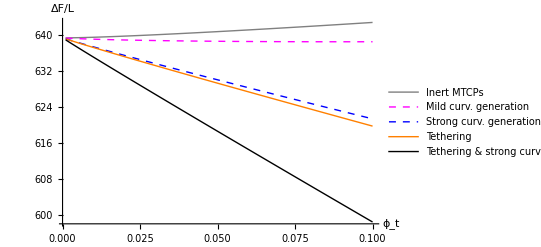

```mathematica
(* We could now add the tethering capability of MCTPs (by setting ϵa0>0) We do it in a general way in the next plots, where we show the optimal free energy of the system including (or not) different contributions from MCTPs (tethering,curvature generation,etc.) *)

Plot[{NMinimize[{(FPD/L)/.{ζMCTP->0.0,ϵa0->0,Rt->(RPM-2 δ-h)}/.parsTOT,0<h<(RPM-6),7≤RPM≤50},{h,RPM},Method->{"RandomSearch","SearchPoints"->10}][[1]],NMinimize[{(FPD/L)/.{ζMCTP->0.1,ϵa0->0}/.parsTOT,0<h<20,2.5≤Rt≤30},{h,Rt},Method->{"RandomSearch","SearchPoints"->10}][[1]],NMinimize[{(FPD/L)/.{ζMCTP->0.5,ϵa0->0,Rt->(RPM-2 δ-h)}/.parsTOT,0<h<(RPM-6),7≤RPM≤50},{h,RPM},Method->{"RandomSearch","SearchPoints"->10}][[1]],NMinimize[{(FPD/L)/.{ζMCTP->0.,ϵa0->10,Rt->(RPM-2 δ-h)}/.parsTOT,0<h<(RPM-6),7≤RPM≤50},{h,RPM},Method->{"RandomSearch","SearchPoints"->10}][[1]],NMinimize[{(FPD/L)/.{ζMCTP->0.5,ϵa0->10,Rt->(RPM-2 δ-h)}/.parsTOT,0<h<(RPM-6),7≤RPM≤50},{h,RPM},Method->{"RandomSearch","SearchPoints"->10}][[1]]},{ϕt,0.001,0.1},AxesLabel->{"ϕ_t","ΔF/L"},PlotStyle->{{Thick,Gray},{Magenta, Thick,Dashed},{Blue,Thick,Dashed},{Orange,Thick},{Thick,Black}},PlotLegends->{"Inert MTCPs","Mild curv. generation","Strong curv. generation","Tethering","Tethering & strong curv."}]
```

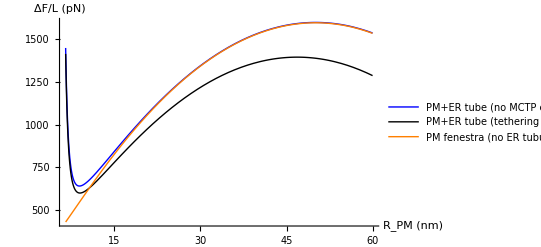

```mathematica
(* And here, the corresponding profile of the total free energy as a function of the PM pore size,again including the three situations;(1) only PM (no ER tube, remember that in this case, although the minimum of the energy has a lower value, the energy barrier that needs to be overcome is smaller than when there is an ER tube–because there needs to be “only” PM pore sealing);
(2) PD with inert MCTPs (no enrichment, no curv. sensing, no tethering);(3) PD with MCTPS that can both tether and sense curvature (in these two latter curves,the energy barrier for full closure is the same - and larger than in the PM only case,because now we have to seal the PM pore AND break or remove the ER tube) *)
Plot[{(Fcellpl/L)/.{Rp->RPM}/.parsTOT},{RPM,6.5,60},AxesLabel->{"R_PM (nm)","ΔF/L (pN)"},AxesOrigin->{0,0},PlotStyle->{{Orange,Thick}},PlotRange->All,PlotLegends->{"PM fenestra (no ER tubule)"}];
Plot[{NMinimize[{(FPD/L)/.{ζMCTP->0.,ϵa0->0,Rt->(RPM-2 δ-h),ϕt->ϕb}/.parsTOT,0<h<(RPM-6)},{h},Method->{"RandomSearch","SearchPoints"->10}][[1]],NMinimize[{(FPD/L)/.{ζMCTP->0.5,ϵa0->10,Rt->(RPM-2 δ-h)}/.parsTOT,0<h<(RPM-6),0≤ϕt≤0.1},{h,ϕt},Method->{"RandomSearch","SearchPoints"->10}][[1]]},{RPM,6.5,60},AxesLabel->{"R_PM (nm)","ΔF/L (pN)"},AxesOrigin->{0,0},PlotStyle->{{Blue,Thick},{Black,Thick}},PlotRange->All,PlotLegends->{"PM+ER tube (no MCTP enrichm.)","PM+ER tube (tethering and curv.gen.)"}];
panelB=Show[%,%%]
```

```mathematica
(*multidat=Cases[First@panelB,Line[data_]:>data,-4];
Export["panelB"<>IntegerString[#2]<>".txt",#,"Table"]&~MapIndexed~multidat*)
```

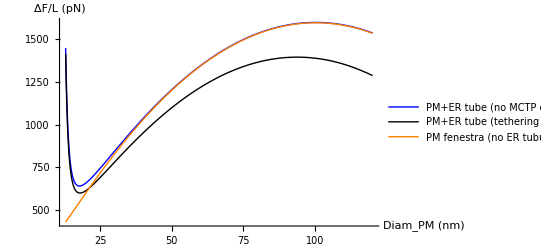

```mathematica
Plot[{(Fcellpl/L)/.{Rp->(DPM/2)}/.parsTOT},{DPM,13,120},AxesLabel->{"Diam_PM (nm)","ΔF/L (pN)"},AxesOrigin->{0,0},PlotStyle->{{Orange,Thick}},PlotRange->All,PlotLegends->{"PM fenestra (no ER tubule)"}];
Plot[{NMinimize[{(FPD/L)/.{ζMCTP->0.,ϵa0->0,Rt->((DPM/2)-2 δ-h),ϕt->ϕb}/.parsTOT,0<h<((DPM/2)-6)},{h},Method->{"RandomSearch","SearchPoints"->10}][[1]],NMinimize[{(FPD/L)/.{ζMCTP->0.5,ϵa0->10,Rt->((DPM/2)-2 δ-h)}/.parsTOT,0<h<((DPM/2)-6),0≤ϕt≤0.1},{h,ϕt},Method->{"RandomSearch","SearchPoints"->10}][[1]]},{DPM,13,120},AxesLabel->{"Diam_PM (nm)","ΔF/L (pN)"},AxesOrigin->{0,0},PlotStyle->{{Blue,Thick},{Black,Thick}},PlotRange->All,PlotLegends->{"PM+ER tube (no MCTP enrichm.)","PM+ER tube (tethering and curv.gen.)"}];
panelBdiam=Show[%,%%]
```

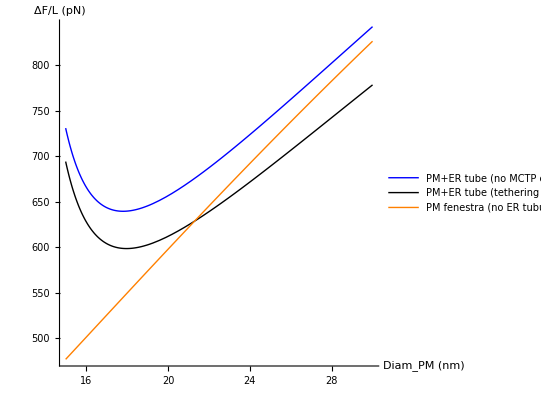

```mathematica
Plot[{(Fcellpl/L)/.{Rp->(DPM/2)}/.parsTOT},{DPM,15,30},AxesLabel->{"Diam_PM (nm)","ΔF/L (pN)"},AxesOrigin->{15,400},PlotStyle->{{Orange,Thick}},PlotRange->All,PlotLegends->{"PM fenestra (no ER tubule)"}];
Plot[{NMinimize[{(FPD/L)/.{ζMCTP->0.,ϵa0->0,Rt->((DPM/2)-2 δ-h),ϕt->ϕb}/.parsTOT,0<h<((DPM/2)-6)},{h},Method->{"RandomSearch","SearchPoints"->10}][[1]],NMinimize[{(FPD/L)/.{ζMCTP->0.5,ϵa0->10,Rt->((DPM/2)-2 δ-h)}/.parsTOT,0<h<((DPM/2)-6),0≤ϕt≤0.1},{h,ϕt},Method->{"RandomSearch","SearchPoints"->10}][[1]]},{DPM,15,30},AxesLabel->{"Diam_PM (nm)","ΔF/L (pN)"},AxesOrigin->{15,400},PlotStyle->{{Blue,Thick},{Black,Thick}},PlotRange->All,PlotLegends->{"PM+ER tube (no MCTP enrichm.)","PM+ER tube (tethering and curv.gen.)"}];
panelBdiamZOOM=Show[%,%%,AspectRatio->1]
```

```mathematica
multidat=Cases[First@panelBdiamZOOM,Line[data_]:>data,-4];
Export["panelBdiamZOOM"<>IntegerString[#2]<>".txt",#,"Table"]&~MapIndexed~multidat
```

{panelBdiamZOOM1.txt,panelBdiamZOOM2.txt,panelBdiamZOOM3.txt}

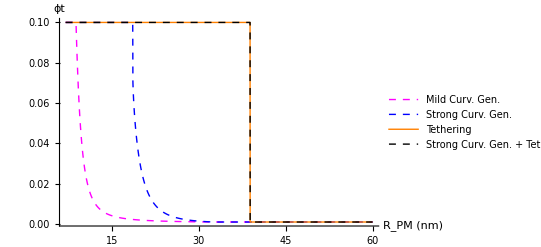

```mathematica
(* This shows how the ER tubules gets enriched with MCTPs while the PM fenestra gets constricted (narrowing values of R_PM) *)
Plot[{ϕt/.NMinimize[{(FPD/L)/.{ζMCTP->0.1,ϵa0->0,Rt->(RPM-2 δ-h)}/.parsTOT,0<h<(RPM-6),0≤ϕt≤0.1,((RPM-2 δ-h)/.parsTOT)≤(Rer0/.parsTOT)},{h,ϕt},Method->{"RandomSearch","SearchPoints"->10}][[2]],
ϕt/.NMinimize[{(FPD/L)/.{ζMCTP->0.5,ϵa0->0,Rt->(RPM-2 δ-h)}/.parsTOT,0<h<(RPM-6),0≤ϕt≤0.1,((RPM-2 δ-h)/.parsTOT)≤(Rer0/.parsTOT)},{h,ϕt},Method->{"RandomSearch","SearchPoints"->20}][[2]],ϕt/.NMinimize[{(FPD/L)/.{ζMCTP->0.,ϵa0->10,Rt->(RPM-2 δ-h)}/.parsTOT,0<h<(RPM-6),0≤ϕt≤0.1,((RPM-2 δ-h)/.parsTOT)≤(Rer0/.parsTOT)},{h,ϕt},Method->{"RandomSearch","SearchPoints"->10}][[2]],ϕt/.NMinimize[{(FPD/L)/.{ζMCTP->0.5,ϵa0->10,Rt->(RPM-2 δ-h)}/.parsTOT,0<h<(RPM-6),0≤ϕt≤0.1,((RPM-2 δ-h)/.parsTOT)≤(Rer0/.parsTOT)},{h,ϕt},Method->{"RandomSearch","SearchPoints"->50}][[2]]},{RPM,7,60},AxesLabel->{"R_PM (nm)","ϕt"},AxesOrigin->{0,0},PlotStyle->{{Magenta,Dashed,Thick},{Blue,Dashed,Thick},{Orange,Thick},{Black,Thick, Dashed}},PlotRange->All,PlotLegends->{"Mild Curv. Gen.","Strong Curv. Gen.","Tethering","Strong Curv. Gen. + Tethering"}]
```

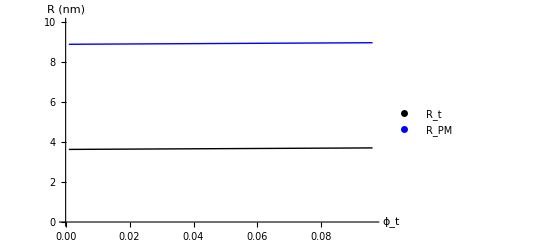

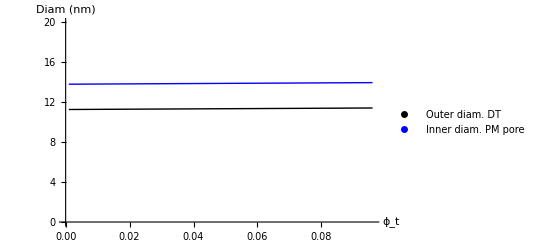

```mathematica
(* And finally the radius (measured in the bilayer midplane) of the ER tubule and the outer diameter of the ER tube, which is twice the midplane radius plus twice the monolayer thickness. *)

ListPlot[{Table[{ϕt,Rt/.NMinimize[{(FPD/L)/.{ζMCTP->0.5,ϵa0->10}/.parsTOT,0<h<10,26≥Rt≥2},{h,Rt},Method->{"RandomSearch","SearchPoints"->10}][[2]]},{ϕt,0.001,0.1,0.005}],Table[{ϕt,(Rt/.NMinimize[{(FPD/L)/.{ζMCTP->0.5,ϵa0->10}/.parsTOT,0<h<10,26≥Rt≥2},{h,Rt},Method->{"RandomSearch","SearchPoints"->10}][[2]])+(h/.NMinimize[{(FPD/L)/.{ζMCTP->0.5,ϵa0->10}/.parsTOT,0<h<10,26≥Rt≥2},{h,Rt},Method->{"RandomSearch","SearchPoints"->10}][[2]])+(2 δ/.parsTOT)},{ϕt,0.001,0.1,0.005}]},AxesLabel->{"ϕ_t","R (nm)"},AxesOrigin->{0,0},PlotStyle->{{Black},{Blue}},PlotRange->{0,10},PlotLegends->{"R_t","R_PM"},Joined->True]

ListPlot[{Table[{ϕt,((2δ)/.parsTOT)+2 (Rt/.NMinimize[{(FPD/L)/.{ζMCTP->0.5,ϵa0->10}/.parsTOT,0<h<10,26≥Rt≥2},{h,Rt},Method->{"RandomSearch","SearchPoints"->10}][[2]])},{ϕt,0.001,0.1,0.005}],Table[{ϕt,((-2 δ)/.parsTOT)+2 ((Rt/.NMinimize[{(FPD/L)/.{ζMCTP->0.5,ϵa0->10}/.parsTOT,0<h<10,26≥Rt≥2},{h,Rt},Method->{"RandomSearch","SearchPoints"->10}][[2]])+(h/.NMinimize[{(FPD/L)/.{ζMCTP->0.5,ϵa0->10}/.parsTOT,0<h<10,26≥Rt≥2},{h,Rt},Method->{"RandomSearch","SearchPoints"->10}][[2]])+(2 δ/.parsTOT))},{ϕt,0.001,0.1,0.005}]},AxesLabel->{"ϕ_t","Diam (nm)"},AxesOrigin->{0,0},PlotStyle->{{Black},{Blue}},PlotRange->{0,20},PlotLegends->{"Outer diam. DT","Inner diam. PM pore"},Joined->True]
```

### Some results on the effect of the constricting force

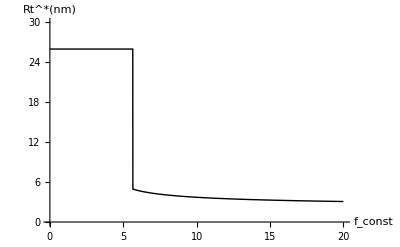

```mathematica
Plot[{Rt/.NMinimize[{(FPD/L)/.{fsp->fx,ζMCTP->0.5,ϵa0->10}/.parsTOT,0<h<10,26≥Rt≥2,0≤ϕt≤0.1},{h,Rt,ϕt},Method->{"RandomSearch","SearchPoints"->10}][[2]]},{fx,0,20},AxesLabel->{"f_const","Rt^*(nm)"},AxesOrigin->{0,0},PlotStyle->{{Black,Thick}},PlotRange->{0,30}]
```